```mathematica
p=10;
n=100;
```

```mathematica
S=With[{μ=ConstantArray[0,p],Σ=DiagonalMatrix[ConstantArray[1,p]]},
RandomVariate[MultinormalDistribution[μ,Σ],n]
];
```

```mathematica
w={9/10}~Join~ConstantArray[1/90,9];
```

```mathematica
d=S.w
```

{0.324497,0.836192,1.09907,0.442647,-2.53438,-0.49019,1.77506,-0.51665,0.267134,-1.04709,0.321487,1.32374,-1.96038,-0.963739,0.207865,0.408029,1.68354,-0.325716,-0.689742,0.814611,-0.25846,-0.111652,1.62467,0.29345,0.622541,1.00464,-0.875881,-0.109972,1.12349,0.758739,0.989132,0.586224,-0.367698,0.802874,1.30951,0.456441,-1.352,-0.0723714,0.0265176,-0.974327,0.146448,-0.191004,0.0246154,-0.559577,0.00194911,2.39697,0.420064,-1.38959,1.19974,-1.11699,-0.317093,0.365917,-0.234698,-1.16001,-1.01985,-0.738891,0.904454,-0.732034,-0.73977,0.37598,0.787286,-0.41615,0.847456,0.0873614,-0.458293,0.552995,-0.0176525,-0.227963,-0.209078,-0.192081,-0.456128,1.21348,0.850788,0.0950283,-1.23601,0.0144386,-0.1522,0.149336,1.85022,0.853373,-0.0000618578,-1.16344,0.357145,-0.149577,0.103529,-2.27856,-0.721984,-0.0995191,-0.56699,-2.06489,1.14319,0.812948,-0.225565,-0.291449,-0.597501,0.180178,-0.435418,-1.03525,-0.565899,0.144405}

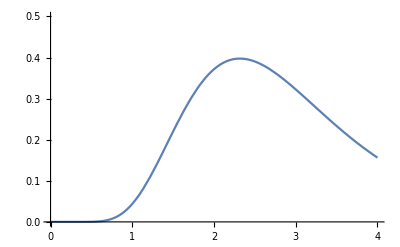

```mathematica
Plot[PDF[LogNormalDistribution[1,0.4],x],{x,0,4},PlotRange->{0,.5}]
```

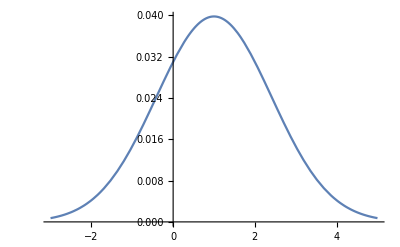

```mathematica
Plot[PDF[NormalDistribution[1,2],x]^2,{x,-3,5}]
```

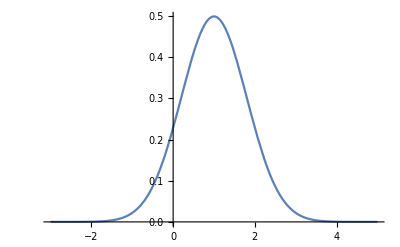

```mathematica
Plot[PDF[NormalDistribution[1,.8],x],{x,-3,5}]
```

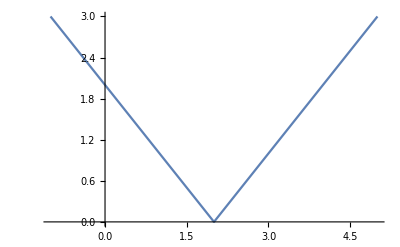

```mathematica
Plot[Abs[x-2],{x,-1,5}]
```

```mathematica
p={{2,-1},
{1,-1}};
```

```mathematica
d={1,1};
```

```mathematica
Plot3D[With[{q={q1,q2}},
Mean@Abs[q.p-d]],
{q1,-5,5},{q2,-5,5}
]
```

-Graphics3D-

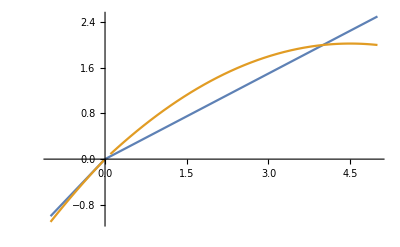

```mathematica
Plot[{x+Min[-0.5x,0],x+Min[-0.1x,0]-0.1Norm[x,2]^2},{x,-1,5}]
```

```mathematica
Norm[2,2]
```

2

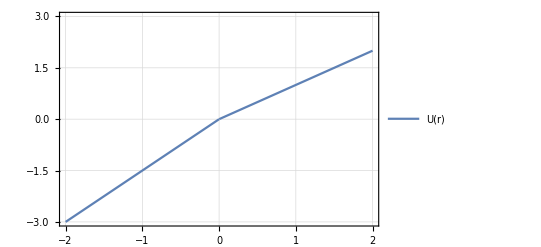

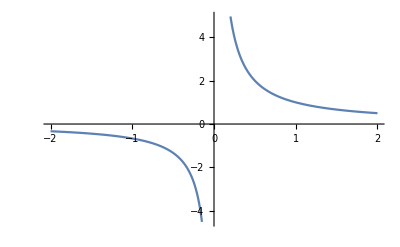

```mathematica
U[r_]:=r+Min[0.5r,0];
Plot[U[r],{r,-2,2},PlotRange->{-3,3},PlotTheme->"Detailed"]
Plot[1/U[r],{r,-2,2}]
```

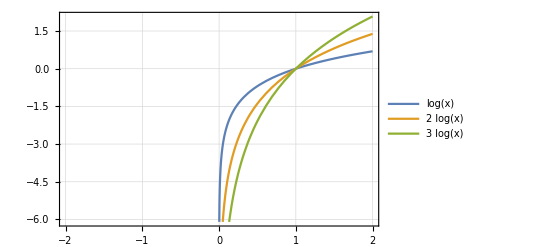

```mathematica
Plot[{Log[x],2Log[x],3Log[x]},{x,-2,2},PlotTheme->"Detailed"]
```

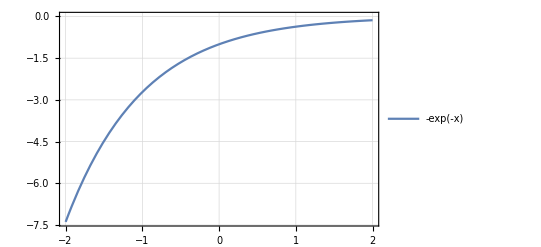

```mathematica
s=Plot[-Exp[-x],{x,-2,2},PlotTheme->"Detailed"]
```

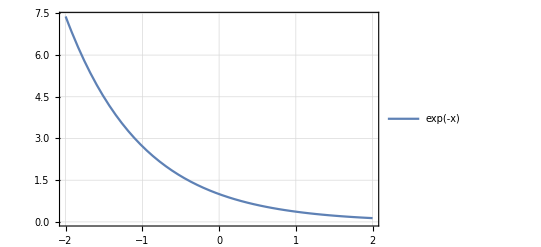

```mathematica
s=Plot[Exp[-x],{x,-2,2},PlotTheme->"Detailed"]
```

```mathematica
Export["/Users/TBM/Desktop/ProjetC/Mai2015/FigExpUtility2.png",s,Background->None,ImageSize->600]
```

/Users/TBM/Desktop/ProjetC/Mai2015/FigExpUtility2.png

```mathematica
U[r_]:=r+Min[0,0.5 r];
```

```mathematica
ExpU[r_]:=-Exp[-r];
```

```mathematica
l[r_,p_]:=
If[r>0,
ExpU[r]-ExpU[p r],
ExpU[0]-ExpU[p r]
];
```

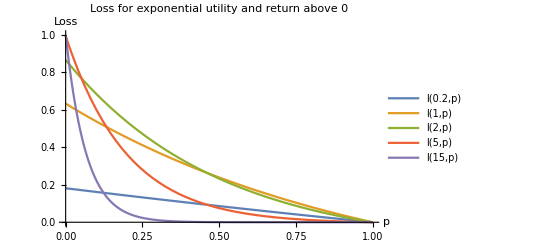

```mathematica
expULossAboveZero=Plot[{l[0.2,p],l[1,p],l[2,p],l[5,p],l[15,p]},{p,0,1},AxesLabel->{p,"Loss"},PlotLegends->"Expressions",PlotLabel->"Loss for exponential utility and return above 0"]
```

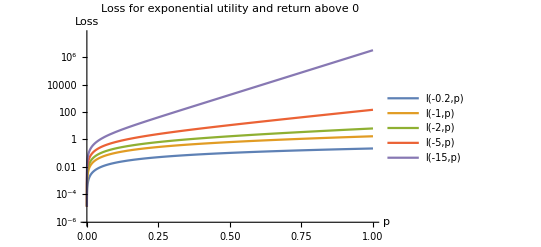

```mathematica
expULossBelowZero=LogPlot[{l[-0.2,p],l[-1,p],l[-2,p],l[-5,p],l[-15,p]},{p,0,1},AxesLabel->{p,"Loss"},PlotLegends->"Expressions",PlotLabel->"Loss for exponential utility and return above 0"]
```

```mathematica
Manipulate[
Plot[l[t][p],{p,0,1},AxesLabel->{p,"Loss"},PlotRange->{0,1}],
{t,-5,15}
]
```

```mathematica
Manipulate[
Plot[l[t][p],{p,0,1},AxesLabel->{p,"Loss"},PlotRange->{0,1}],
{t,-15,0}
]
```

```mathematica
Export["/Users/TBM/Desktop/ProjetC/Mai2015/expULossAboveZero.png",expULossAboveZero,Background->None,ImageSize->600]
```

/Users/TBM/Desktop/ProjetC/Mai2015/expULossAboveZero.png

```mathematica
w=.
```